## localised bulging of an inflated membrane tube weakly nonlinear behaviour based on the exact membrane theory and the 1D gradient model

Prepared by Yibin Fu (y.fu@keele.ac.uk) for the advanced summer schools 2022 at CISM

### Governing equations

```mathematica
Gent97sub={W->Function[{x,y},-1/2 * (972/10) Log[1-(x^2+y^2+x^-2 y^-2-3)/(972/10)]]};
halflength=4;

λ2[Z_]=√(r'[Z]^2+zd[Z]^2);  (*zd means z'[Z]*)
eqn1=(Derivative[0,1][W][r[Z],λ2[Z]])/λ2[Z]*zd[Z]-1/2 P r[Z]^2;  (*eqn Subscript[(3.3), 2] with N=0. The case of non-zero N can similarly be analysed *)
eqn2=Derivative[1,0][W][r[Z],λ2[Z]]-D[(Derivative[0,1][W][r[Z],λ2[Z]])/λ2[Z] r'[Z],Z]-P r[Z] zd[Z]; (*eqn Subscript[(3.3), 1]*)
r[Z_]=r∞+ϵ r1[Z]+ϵ^2 r2[Z]+ϵ^3 r3[Z];  (* expansion for weakly nonlinear analysis *)
zd[Z_]=z∞+ϵ zd1[Z]+ϵ^2 zd2[Z]+ϵ^3 zd3[Z];
eqn1a=Series[eqn1,{ϵ,0,3}];  (* it is sufficient to expand the two governing equations to order ϵ^3*)
eqn2a=Series[eqn2,{ϵ,0,3}];
```

### Weakly nonlinear analysis

```mathematica
(*note that eqn1 is an algebraic equation for zd[Z]. As a result, zd1, zd2 etc are determined by solving algebraic equations at successive orders *)
```

#### Leading order

```mathematica
eqn11=Coefficient[eqn1a,ϵ]
```

-P r∞ r1[Z]+(√((z∞)^2) zd1[Z] W^(0,2)[r∞,√((z∞)^2)]+z∞ r1[Z] W^(1,1)[r∞,√((z∞)^2)])/(√((z∞)^2))

```mathematica
zd1[Z_]=Simplify[zd1[Z]/.Solve[eqn11==0,zd1[Z]][[1]],z∞>0]
```

(r1[Z] (P r∞-W^(1,1)[r∞,z∞]))/(W^(0,2)[r∞,z∞])

```mathematica
eqn21=Simplify[Coefficient[eqn2a,ϵ],z∞>0]
```

-(r1''[Z] W^(0,1)[r∞,z∞])/(z∞)+r1[Z] (-P z∞-((-P r∞+W^(1,1)[r∞,z∞])^2)/(W^(0,2)[r∞,z∞])+W^(2,0)[r∞,z∞])

```mathematica
codd=Coefficient[eqn21,r1''[Z]]
```

-(W^(0,1)[r∞,z∞])/(z∞)

```mathematica
leading=Simplify[eqn21/codd/.P->(Derivative[1,0][W][r∞,z∞])/(r∞ z∞)]
```

r1''[Z]-(z∞ r1[Z] (-(W^(1,0)[r∞,z∞])/(r∞)-((-(W^(1,0)[r∞,z∞])/(z∞)+W^(1,1)[r∞,z∞])^2)/(W^(0,2)[r∞,z∞])+W^(2,0)[r∞,z∞]))/(W^(0,1)[r∞,z∞])

```mathematica
result1=Together[Coefficient[leading,r1[Z]]]
```

((z∞)^2 W^(0,2)[r∞,z∞] W^(1,0)[r∞,z∞]+r∞ (W^(1,0)[r∞,z∞])^2-2 r∞ z∞ W^(1,0)[r∞,z∞] W^(1,1)[r∞,z∞]+r∞ (z∞)^2 (W^(1,1)[r∞,z∞])^2-r∞ (z∞)^2 W^(0,2)[r∞,z∞] W^(2,0)[r∞,z∞])/(r∞ z∞ W^(0,1)[r∞,z∞] W^(0,2)[r∞,z∞])

```mathematica
omega=(-r∞ (Derivative[1,0][W][r∞,z∞]-z∞ Derivative[1,1][W][r∞,z∞])^2+(z∞)^2 Derivative[0,2][W][r∞,z∞] (-Derivative[1,0][W][r∞,z∞]+r∞ Derivative[2,0][W][r∞,z∞]))/(r∞ z∞ Derivative[0,1][W][r∞,z∞] Derivative[0,2][W][r∞,z∞]);
Simplify[result1+omega]  (*not surprisingly, the bifurcation condition obtained here is the same as that derived in fig-3&4.nb*)
```

0

```mathematica
omega/.{Derivative[1,0][W][r∞,z∞]->Subscript[W, 1],Derivative[0,1][W][r∞,z∞]->Subscript[W, 2],Derivative[1,1][W][r∞,z∞]->Subscript[W, 12],Derivative[0,2][W][r∞,z∞]->Subscript[W, 22],Derivative[2,0][W][r∞,z∞]->Subscript[W, 11],r∞->Subscript[λ, 1],z∞->Subscript[λ, 2]}
```

(W_22 (-W_1+W_11 λ_1) λ_2^2-λ_1 (W_1-W_12 λ_2)^2)/(W_2 W_22 λ_1 λ_2)

```mathematica
Force=Derivative[0,1][W][r∞,z∞]-(r∞ Derivative[1,0][W][r∞,z∞])/(2*z∞);
```

```mathematica
nn=Simplify[Force/.Gent97sub]
```

(243 (1+(r∞)^4 (z∞)^2-2 (r∞)^2 (z∞)^4))/(z∞ (5+5 (r∞)^4 (z∞)^2+(r∞)^2 (z∞)^2 (-501+5 (z∞)^2)))

```mathematica
zf[r∞_]=z∞/.Solve[nn==0, z∞][[4]]
```

1/2 √((r∞)^2+(√(8+(r∞)^6))/(r∞))

#### Second order

```mathematica
eqn21=Simplify[Coefficient[eqn1a,ϵ^2],z∞>0]
```

1/2 (2 zd2[Z] W^(0,2)[r∞,z∞]+(r1'[Z]^2 (-W^(0,1)[r∞,z∞]+z∞ W^(0,2)[r∞,z∞]))/(z∞)^2+2 r2[Z] (-P r∞+W^(1,1)[r∞,z∞])+(r1[Z]^2 W^(0,3)[r∞,z∞] (-P r∞+W^(1,1)[r∞,z∞])^2)/((W^(0,2)[r∞,z∞])^2)+(2 r1[Z]^2 (P r∞-W^(1,1)[r∞,z∞]) W^(1,2)[r∞,z∞])/(W^(0,2)[r∞,z∞])+r1[Z]^2 (-P+W^(2,1)[r∞,z∞]))

```mathematica
zd2[Z_]=Simplify[zd2[Z]/.Solve[eqn21==0,zd2[Z]][[1]],z∞>0]
```

1/(2 (W^(0,2)[r∞,z∞])^3)(((W^(0,2)[r∞,z∞])^2 (r1'[Z]^2 (W^(0,1)[r∞,z∞]-z∞ W^(0,2)[r∞,z∞])+2 (z∞)^2 r2[Z] (P r∞-W^(1,1)[r∞,z∞])))/(z∞)^2-r1[Z]^2 (W^(0,3)[r∞,z∞] (-P r∞+W^(1,1)[r∞,z∞])^2+2 W^(0,2)[r∞,z∞] (P r∞-W^(1,1)[r∞,z∞]) W^(1,2)[r∞,z∞]+(W^(0,2)[r∞,z∞])^2 (-P+W^(2,1)[r∞,z∞])))

```mathematica
eqn22=Simplify[Coefficient[eqn2a/.P->(Derivative[1,0][W][r∞,z∞])/(r∞ z∞),ϵ^2],z∞>0]
```

-1/(2 r∞ (z∞)^3 (W^(0,2)[r∞,z∞])^3)(2 r∞ (z∞)^2 r2''[Z] W^(0,1)[r∞,z∞] (W^(0,2)[r∞,z∞])^3-2 r∞ r1[Z] r1''[Z] W^(0,1)[r∞,z∞] (W^(0,2)[r∞,z∞])^2 W^(1,0)[r∞,z∞]+2 (z∞)^3 r2[Z] (W^(0,2)[r∞,z∞])^3 W^(1,0)[r∞,z∞]+2 r∞ z∞ r1[Z] r1''[Z] (W^(0,2)[r∞,z∞])^3 W^(1,0)[r∞,z∞]+3 z∞ r1[Z]^2 (W^(0,2)[r∞,z∞])^2 (W^(1,0)[r∞,z∞])^2+2 r∞ z∞ r2[Z] (W^(0,2)[r∞,z∞])^2 (W^(1,0)[r∞,z∞])^2-r∞ r1[Z]^2 W^(0,3)[r∞,z∞] (W^(1,0)[r∞,z∞])^3+2 r∞ z∞ r1[Z] r1''[Z] W^(0,1)[r∞,z∞] (W^(0,2)[r∞,z∞])^2 W^(1,1)[r∞,z∞]-3 (z∞)^2 r1[Z]^2 (W^(0,2)[r∞,z∞])^2 W^(1,0)[r∞,z∞] W^(1,1)[r∞,z∞]-4 r∞ (z∞)^2 r2[Z] (W^(0,2)[r∞,z∞])^2 W^(1,0)[r∞,z∞] W^(1,1)[r∞,z∞]+3 r∞ z∞ r1[Z]^2 W^(0,3)[r∞,z∞] (W^(1,0)[r∞,z∞])^2 W^(1,1)[r∞,z∞]+2 r∞ (z∞)^3 r2[Z] (W^(0,2)[r∞,z∞])^2 (W^(1,1)[r∞,z∞])^2-3 r∞ (z∞)^2 r1[Z]^2 W^(0,3)[r∞,z∞] W^(1,0)[r∞,z∞] (W^(1,1)[r∞,z∞])^2+r∞ (z∞)^3 r1[Z]^2 W^(0,3)[r∞,z∞] (W^(1,1)[r∞,z∞])^3+r∞ r1'[Z]^2 (W^(0,2)[r∞,z∞])^2 (z∞ W^(0,2)[r∞,z∞] W^(1,0)[r∞,z∞]+W^(0,1)[r∞,z∞] (-W^(1,0)[r∞,z∞]+z∞ W^(1,1)[r∞,z∞]))-3 r∞ z∞ r1[Z]^2 W^(0,2)[r∞,z∞] (W^(1,0)[r∞,z∞])^2 W^(1,2)[r∞,z∞]+6 r∞ (z∞)^2 r1[Z]^2 W^(0,2)[r∞,z∞] W^(1,0)[r∞,z∞] W^(1,1)[r∞,z∞] W^(1,2)[r∞,z∞]-3 r∞ (z∞)^3 r1[Z]^2 W^(0,2)[r∞,z∞] (W^(1,1)[r∞,z∞])^2 W^(1,2)[r∞,z∞]-2 r∞ (z∞)^3 r2[Z] (W^(0,2)[r∞,z∞])^3 W^(2,0)[r∞,z∞]-3 r∞ (z∞)^2 r1[Z]^2 (W^(0,2)[r∞,z∞])^2 W^(1,0)[r∞,z∞] W^(2,1)[r∞,z∞]+3 r∞ (z∞)^3 r1[Z]^2 (W^(0,2)[r∞,z∞])^2 W^(1,1)[r∞,z∞] W^(2,1)[r∞,z∞]-r∞ (z∞)^3 r1[Z]^2 (W^(0,2)[r∞,z∞])^3 W^(3,0)[r∞,z∞])

```mathematica
eqn22=eqn22/codd;
```

```mathematica
Simplify[Coefficient[eqn22,r2''[Z]]]
```

1

```mathematica
Simplify[Coefficient[-eqn22, r2[Z]]-omega]
```

0

```mathematica
cor1r1dd=Simplify[Coefficient[-eqn22,r1[Z] r1''[Z]]]
```

(-(z∞ W^(1,0)[r∞,z∞])/(W^(0,1)[r∞,z∞])+(W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])/(W^(0,2)[r∞,z∞]))/(z∞)^2

```mathematica
cor12=Simplify[Coefficient[-eqn22,r1[Z]^2]]
```

(r∞ W^(0,3)[r∞,z∞] (W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])^3+3 r∞ z∞ W^(0,2)[r∞,z∞] (W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])^2 W^(1,2)[r∞,z∞]-3 z∞ (W^(0,2)[r∞,z∞])^2 (W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞]) (W^(1,0)[r∞,z∞]-r∞ z∞ W^(2,1)[r∞,z∞])+r∞ (z∞)^3 (W^(0,2)[r∞,z∞])^3 W^(3,0)[r∞,z∞])/(2 r∞ (z∞)^2 W^(0,1)[r∞,z∞] (W^(0,2)[r∞,z∞])^3)

```mathematica
cor1d2=Simplify[Coefficient[-eqn22,r1'[Z]^2]]
```

(-(z∞ W^(1,0)[r∞,z∞])/(W^(0,1)[r∞,z∞])+(W^(1,0)[r∞,z∞]-z∞ W^(1,1)[r∞,z∞])/(W^(0,2)[r∞,z∞]))/(2 (z∞)^2)

```mathematica
check=Simplify[r2''[Z]-omega r2[Z]-cor1r1dd  r1[Z] r1''[Z]-cor12  r1[Z]^2 -cor1d2  r1'[Z]^2-eqn22]
```

0

Thus, the second order equation is given by r2''[Z]=omega r2[Z]+cor1r1dd  r1[Z] r1''[Z]+cor12  r1[Z]^2 +cor1d2  r1'[Z]^2

```mathematica
r1[Z_]=1/2 A (E^(I k Z)+E^(-I k Z));
r2[Z_]=A^2*(q0+q1 E^(2I k Z)+q1 E^(-2I k Z));
eq2=r2''[Z]-omega0 r2[Z]-cor1r1dd0  r1[Z] r1''[Z]-cor120  r1[Z]^2 -cor1d20  r1'[Z]^2;
```

```mathematica
temp1=Collect[Simplify[eq2],{E^(2I k Z), E^(-2I k Z) }]
```

-1/4 A^2 (2 cor120+2 cor1d20 k^2-2 cor1r1dd0 k^2+4 omega0 q0)-1/4 A^2 ⅇ^(-2 ⅈ k Z) (cor120-cor1d20 k^2-cor1r1dd0 k^2+16 k^2 q1+4 omega0 q1)-1/4 A^2 ⅇ^(2 ⅈ k Z) (cor120-cor1d20 k^2-cor1r1dd0 k^2+16 k^2 q1+4 omega0 q1)

```mathematica
q1=q1/.Solve[Coefficient[temp1, ⅇ^(2 ⅈ k Z)]==0, q1][[1]]
```

(-cor120+cor1d20 k^2+cor1r1dd0 k^2)/(4 (4 k^2+omega0))

```mathematica
q0=q0/.Solve[Simplify[temp1]==0, q0][[1]]
```

(-cor120-cor1d20 k^2+cor1r1dd0 k^2)/(2 omega0)

```mathematica
subWs={Derivative[1,0][W][r∞,z∞]->Subscript[W, 1], Derivative[0,1][W][r∞,z∞]->Subscript[W, 2],Derivative[2,0][W][r∞,z∞]->Subscript[W, 11],Derivative[1,1][W][r∞,z∞]->Subscript[W, 12],Derivative[0,2][W][r∞,z∞]->Subscript[W, 22],Derivative[3,0][W][r∞,z∞]->Subscript[W, 111],Derivative[2,1][W][r∞,z∞]->Subscript[W, 112],Derivative[1,2][W][r∞,z∞]->Subscript[W, 122],Derivative[0,3][W][r∞,z∞]->Subscript[W, 222]};
```

```mathematica
omega/.subWs
```

(-r∞ (W_1-z∞ W_12)^2+(z∞)^2 (-W_1+r∞ W_11) W_22)/(r∞ z∞ W_2 W_22)

```mathematica
subW22=Solve[(-r∞ (Subscript[W, 1]-z∞ Subscript[W, 12])^2+(z∞)^2 (-Subscript[W, 1]+r∞ Subscript[W, 11]) Subscript[W, 22])/(r∞ z∞ Subscript[W, 2] Subscript[W, 22])-ω==0, Subscript[W, 22]][[1]]
```

{W_22→-(r∞ (-W_1+z∞ W_12)^2)/(z∞ (z∞ W_1+r∞ ω W_2-r∞ z∞ W_11))}

```mathematica
Simplify[q0/.{omega0->omega, cor1r1dd0 ->cor1r1dd, cor120->cor12, cor1d20->cor1d2}/.subWs]
```

(r∞ W_2 W_22 (k^2 (-(z∞ W_1)/W_2+(W_1-z∞ W_12)/W_22)-(r∞ (z∞)^3 W_22^3 W_111-3 z∞ (W_1-z∞ W_12) W_22^2 (W_1-r∞ z∞ W_112)+3 r∞ z∞ (W_1-z∞ W_12)^2 W_22 W_122+r∞ (W_1-z∞ W_12)^3 W_222)/(r∞ W_2 W_22^3)))/(4 (-r∞ z∞ (W_1-z∞ W_12)^2+(z∞)^3 (-W_1+r∞ W_11) W_22))

```mathematica
Simplify[q1/.{omega0->omega, cor1r1dd0 ->cor1r1dd, cor120->cor12, cor1d20->cor1d2}/.subWs]
```

(3 k^2 (-(z∞ W_1)/W_2+(W_1-z∞ W_12)/W_22)-(r∞ (z∞)^3 W_22^3 W_111-3 z∞ (W_1-z∞ W_12) W_22^2 (W_1-r∞ z∞ W_112)+3 r∞ z∞ (W_1-z∞ W_12)^2 W_22 W_122+r∞ (W_1-z∞ W_12)^3 W_222)/(r∞ W_2 W_22^3))/(8 (z∞)^2 (4 k^2+(z∞ (-W_1+r∞ W_11))/(r∞ W_2)-(W_1-z∞ W_12)^2/(z∞ W_2 W_22)))

#### Third order

```mathematica
eqn31=Simplify[Coefficient[eqn1a,ϵ^3],z∞>0];
```

```mathematica
zd3[Z_]=Simplify[zd3[Z]/.Solve[eqn31==0,zd3[Z]][[1]],z∞>0];
```

```mathematica
eqn32=Simplify[Coefficient[eqn2a/codd/.P->(Derivative[1,0][W][r∞,z∞])/(r∞ z∞),ϵ^3],z∞>0];
```

```mathematica
Coefficient[eqn32, r3''[Z]]
```

1

Note that after expansions, the second equation eqn2=0 can be written in the form 
ϵ (r1’’-ω r1)+ϵ^2 (r2’’-ω r2+... )+ϵ^3 (r3’’-ω r3+ ...)+..., where the “...” in the round brackets denote nonlinear terms
With r∞=r_cr1+ϵ^2r0 and  ω=ω[r_cr1]+dω ϵ^2r0+..., where where dω=ω’[r_cr1], the first term ϵ (r1’’-ω r1) will give an extra term -ϵ^3 dω r0 r1[Z], which must be added to the third equation, . Thus, the governing equation at order ϵ^3 should take the form eqn32- ω’ r0 r1[Z]=0.

```mathematica
eqn32=eqn32-dω r0 r1[Z];
```

```mathematica
ef1=Coefficient[eqn32,E^(I k Z)];ef3=Coefficient[eqn32,E^(3I k Z)];
```

```mathematica
check=Simplify[ef1 (E^(I k Z)+E^(-I k Z))+ef3 (E^(3I k Z)+E^(-3I k Z))-eqn32+r3''[Z]-omega r3[Z]]
```

0

```mathematica
amplitude=Simplify[ef1 /.{omega0->omega, cor1r1dd0 ->cor1r1dd, cor120->cor12, cor1d20->cor1d2}/.Gent97sub];
coA3=Coefficient[amplitude,A^3];
```

```mathematica
check=Simplify[amplitude/.{r∞->1.1, z∞->1.3, k->0.1}]
```

1.19142 A^3-0.5 A dω r0

### Check the sign of the coefficient of A^3 for different values of L

```mathematica
(*The following is the bifurcation condition (3.32) *)
```

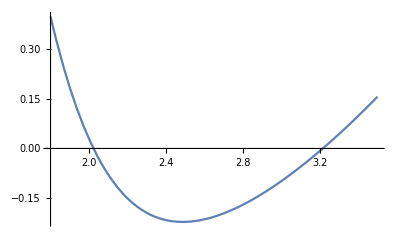

```mathematica
Plot[(Pi/3)^2+omega/.Gent97sub/.{z∞->zf[r∞]}, {r∞,1.8,3.5}]
```

```mathematica
FindRoot[((Pi/3)^2+omega/.Gent97sub/.{z∞->zf[r∞]})==0,{r∞,2}]
```

{r∞→2.02333}

```mathematica
data={};rguess=2.233305250187024;
Do[L=3+i*0.1; rcr1=r∞/.FindRoot[((Pi/L)^2+omega/.Gent97sub/.{z∞->zf[r∞]})==0,{r∞,rguess}];rguess=rcr1;dω=(D[omega/.Gent97sub/.{z∞->zf[r∞]},r∞])/.r∞->rcr1;kcr=Pi/L;kcr=Pi/L; coeff=coA3/.z∞->zf[r∞]/.r∞->rcr1/.k->kcr; data=Append[data,{L, coeff}],{i,0,150}]
```

```mathematica
(*The following plot shows that the coefficient is always negative, meaning that bifurcated solution only exists for r∞>rcr1, which corresponds to P<Subscript[P, cr] on the descending branch of the P vs v curve in uniform inflation *)
```

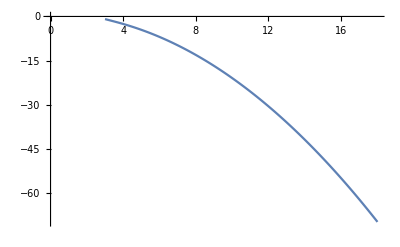

```mathematica
ListPlot[data,Joined->True]
```

We next find the weakly nonlinear solution for a particular L and δ (=ϵ^2 r0=r∞-r_cr1)

```mathematica
L=halflength; rcr1=r∞/.FindRoot[((Pi/L)^2+omega/.Gent97sub/.{z∞->zf[r∞]})==0,{r∞,2.22}]
δ=0.001;
kcr=Pi/L;
```

1.76951

```mathematica
dω=(D[omega/.Gent97sub/.{z∞->zf[r∞]},r∞])/.r∞->rcr1
```

-2.74478

```mathematica
tt=Simplify[amplitude/.z∞->zf[r∞]/.r∞->rcr1/.k->kcr/.{A->ϵA/ϵ, r0->δ/ϵ^2}]  (* ϵA is the actual amplitude *)
```

(0.00137239 ϵA-2.55025 ϵA^3)/ϵ^3

```mathematica
tt=Simplify[tt ϵ^3/ϵA]
```

0.00137239-2.55025 ϵA^2

```mathematica
q0=q0/.{omega0->omega, cor1r1dd0 ->cor1r1dd, cor120->cor12, cor1d20->cor1d2}/.Gent97sub/.z∞->zf[r∞]/.r∞->rcr1/.k->kcr;
q1=q1/.{omega0->omega, cor1r1dd0 ->cor1r1dd, cor120->cor12, cor1d20->cor1d2}/.Gent97sub/.z∞->zf[r∞]/.r∞->rcr1/.k->kcr;
```

```mathematica
ϵA=ϵA/.Solve[tt==0, ϵA][[2]]
```

0.0231978

```mathematica
yweak=Simplify[ϵA Cos[kcr x]+ϵA^2(q0+2 q1 Cos[2 kcr x])]  (*this is the weakly nonlinear solution(3.35)in Fu's notes *)
```

-0.00083612+0.0231978 Cos[(π x)/4]+0.00023202 Cos[(π x)/2]

### Gradient model

```mathematica
gfun[x_?NumericQ]:=y/.FindRoot[(Derivative[0,1][W][x,y]/.Gent97sub)-1/2 pp x^2==0,{y,1.5}]  (* eqn (3.21) with N=0. It defines Subscript[λ, 2] as a function of Subscript[λ, 1]. Wit the use of NumericQ, this function is as good as an explicit expression, e.g. it can be differentiated *)
```

```mathematica
(* The gradient model (3.25) is of the form r''=m1(r)+m2(r) (r')^2 *)
```

```mathematica
gd=(pp x-Derivative[1,1][W][x,gfun[x]])/(Derivative[0,2][W][x,gfun[x]]);  (* eqn (3.26) *)
m1[x_]=gfun[x]/(Derivative[0,1][W][x,gfun[x]])*(Derivative[1,0][W][x,gfun[x]]-pp x gfun[x])/.Gent97sub;
m2[x_]=1/(2 gfun[x] Derivative[0,1][W][x,gfun[x]])*(Derivative[0,1][W][x,gfun[x]] gd-Derivative[1,1][W][x,gfun[x]]-Derivative[0,2][W][x,gfun[x]] gfun[x] gd)/.Gent97sub;
```

```mathematica
pp=((Derivative[1,0][W][r∞,z∞])/(r∞ z∞))/.Gent97sub/.{r∞->(rcr1+δ),z∞->zf[rcr1+δ]}
```

0.743162

#### Finite difference solutions

```mathematica
(* (A[j+1]-2A[j]+A[j-1])/h^2=m1[j]+m2[j] ((A[j+1]-A[j-1])/(2h))^2   *)
```

```mathematica
n=100;  (*number of grid points*)
h=L/n;
sArray=Array[s,n+1,0] ;  (*giving s[0], s[1], ..., s[n] *)
AArray=Array[A,n+2,-1];(*giving A[-1], A[0], s[1], ..., s[n+1] *)
Table[s[j]=j h,{j,0,n}];  (*s[0]=0, s[1]=h, ..., s[n]=L *)
(*The following is the FD equation at the jth node *)
eqslhs[j_]:=(A[j+1]-2A[j]+A[j-1])/h^2-m1[A[j]]-m2[A[j]] ((A[j+1]-A[j-1])/(2h))^2;
A[-1]=A[1]; A[n+1]=A[n-1];
eqs=Table[eqslhs[j]==0,{j,0,n}];
Aguess[x_]= rcr1+δ+yweak; (* We use the weakly nonlinear solution as the guess solution *)
guess=Table[{A[j],Aguess[s[j]]},{j,0,n}];
Afdmsub=FindRoot[eqs,guess];

Afdm=Interpolation[Table[{s[j],A[j]/.Afdmsub},{j,0,n}]];
```

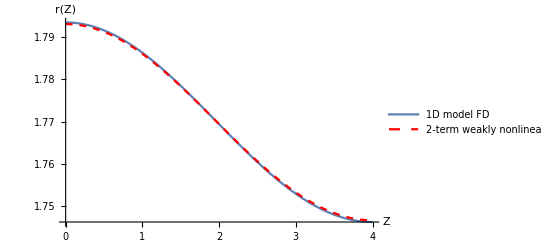

```mathematica
fig1=Plot[{Afdm[s],Aguess[s]},{s,0,L},PlotRange->Full,PlotLegends->Placed[{"1D model FD","2-term weakly nonlinear"},{0.7,0.85}],PlotStyle->{{},{Red,Dashed}},AxesLabel->{Style["Z",FontSize->22,FontColor->Black,FontFamily->"Cambria Math"],Style["r(Z)",FontSize->22,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->Black,TicksStyle->Directive[Black,14]]
```

#### Do loop to follow the evolution of the bulging solution

```mathematica
δmax=3.507549132611972-rcr1  (* this δmax is based on the infinite length assumption *)
```

1.73804

```mathematica
Do[δ=0.001+i*(δmax-0.001)/200;pp=((Derivative[1,0][W][r∞,z∞])/(r∞ z∞))/.Gent97sub/.{r∞->(rcr1+δ),z∞->zf[rcr1+δ]};
eqs=Table[eqslhs[j]==0,{j,0,n}];
Afdmsub=FindRoot[eqs,guess]; data=Append[data,{rcr1+δ, (A[0])/.Afdmsub}];
guess=Table[{A[j],A[j]/.Afdmsub},{j,0,n}],
 {i,0,200}]
```

```mathematica
{rcr1+δ, zf[rcr1+δ]}
```

{3.50755,2.48154}

```mathematica
(Derivative[1,0][W][r∞,z∞])/(r∞ z∞)/.Gent97sub/.{r∞->(rcr1), z∞->zf[rcr1]}
```

0.743321

```mathematica
(Derivative[1,0][W][r∞,z∞])/(r∞ z∞)/.Gent97sub/.{r∞->(rcr1+δ), z∞->zf[rcr1+δ]}
```

0.478761

```mathematica
{rcr1, zf[rcr1]}
```

{1.76951,1.28906}

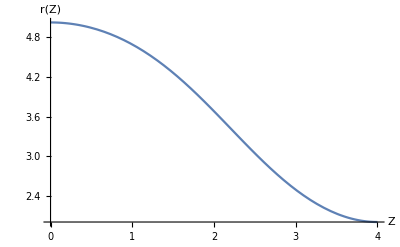

```mathematica
Afdm=Interpolation[Table[{s[j],A[j]/.Afdmsub},{j,0,n}]];fig1=Plot[{Afdm[s]},{s,0,L},PlotRange->Full,PlotStyle->{{},{Red,Dashed}},AxesLabel->{Style["Z",FontSize->22,FontColor->Black,FontFamily->"Cambria Math"],Style["r(Z)",FontSize->22,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->Black,TicksStyle->Directive[Black,14]]
```